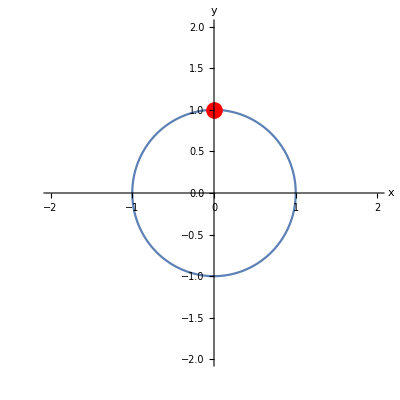

```mathematica
circle = ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
top = Graphics[{Red,PointSize[0.03],Point[{0,1}]}]
Show[circle, top]
```

Sin[2 t]

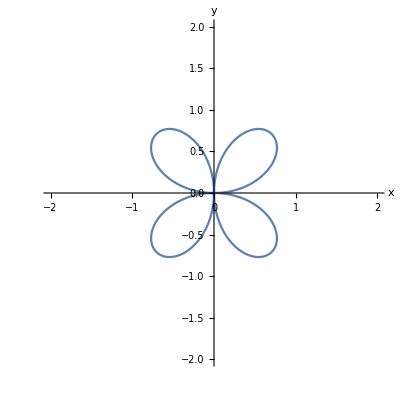

```mathematica
r = Sin[2t]
ParametricPlot[{ r * Cos[t], r* Sin[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
```

Sin[0.5 t]

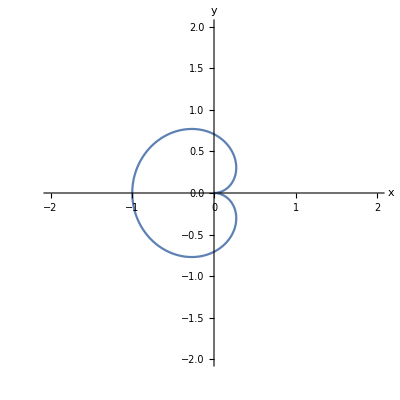

```mathematica
r = Sin[0.5t]
ParametricPlot[{ r * Cos[t], r* Sin[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
```

1

Sin[0.5 t]

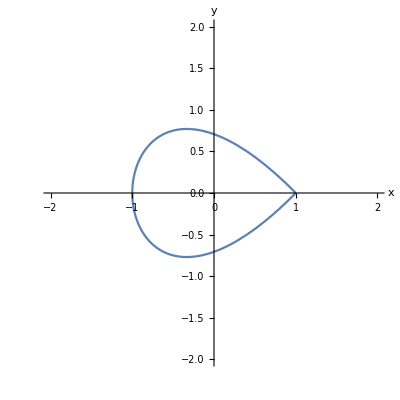

```mathematica
fatness = 1
r = fatness  * Sin[0.5t]
ParametricPlot[{ Cos[t], r*Sin[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
```

2

2 Sin[0.5 t]

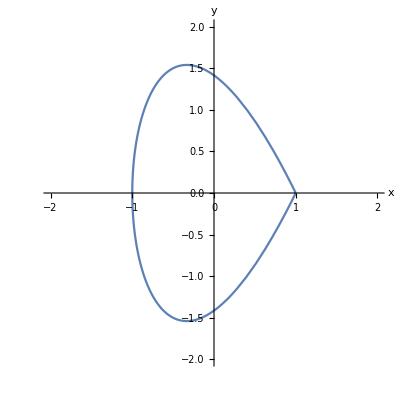

```mathematica
fatness = 2
r = fatness  * Sin[0.5t]
ParametricPlot[{ Cos[t], r * Sin[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
```

1

1

Sin[t/2]

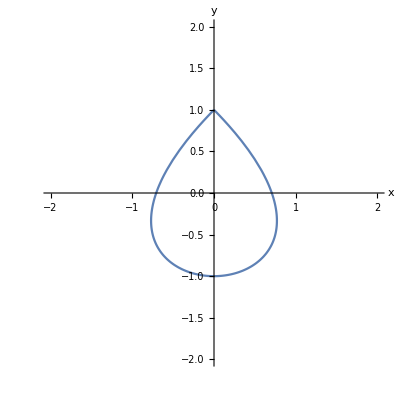

```mathematica
circleRadius = 1
fatness = 1
r = fatness  * Sin[(circleRadius / 2) * t]
ParametricPlot[{ circleRadius * r * Sin[t], circleRadius * Cos[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
```

0.5

1

0

1

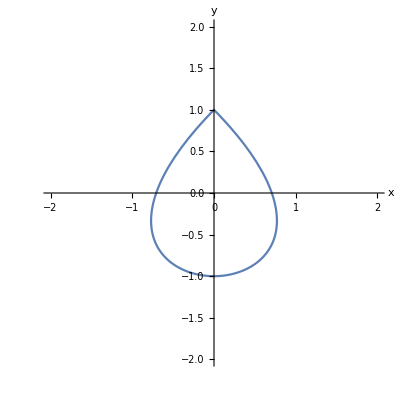

```mathematica
fatness = 0.5
radius = 1
x0 = 0
y0= radius
(* radius of x axis Abs[√((x0 - Cos[t])^2 + (y0 - Sin[t])^2)]: the distance from current point to top point of a droplet (x0, y0) *)
ParametricPlot[{  (√((x0 - radius * Cos[t])^2 + (y0 - radius * Sin[t])^2))* fatness* radius * Cos[t],  radius * Sin[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
```

```mathematica
Animate[ParametricPlot[{  (√((0- 1 * Cos[t])^2 + (1  - 1 * Sin[t])^2))* fatness* 1 * Cos[t],  1 * Sin[t] - (fatness - 0.5)}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}], {fatness, 0.4, 1.0}]
```

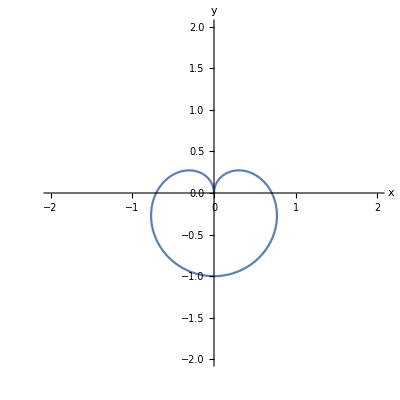

```mathematica
ParametricPlot[{  (√((x0 - radius * Cos[t])^2 + (y0 - radius * Sin[t])^2))* fatness* radius * Cos[t],  (√((x0 - radius * Cos[t])^2 + (y0 - radius * Sin[t])^2))* fatness*radius * Sin[t]}, {t, 0, 2Pi},PlotRange->{{-2, 2}, {-2, 2}}, AxesLabel->{"x", "y"}]
```